```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

/Users/germanv/Documents/GitHub/mmtour

```mathematica
(* Get the command definitions that will be formatted as a package *)
```

```mathematica
<<"mmtour.wl";
```

```mathematica
(* get data for this example *)
```

```mathematica
z20Data=Import["data/z20out.CSV"];
z20Datain=Import["data/z20in.CSV"];
```

## Slicing

```mathematica
This is a saved projection matrix that gives a good view of the z20 data
```

a^2 data gives good is matrix of projection saved that the This view z20

```mathematica
A3old = {{-0.5225163357086493, -0.8222573406979908}, {-0.7104786118356747, 0.5546100076369982}, {-0.04898160937146142, 0.11022563637442358}, 
   {0.4688257917233654, -0.06442758867915532}}
```

{{-0.522516,-0.822257},{-0.710479,0.55461},{-0.0489816,0.110226},{0.468826,-0.0644276}}

SlicePlot can get slices of multiple data sets and plot them on the same axes.

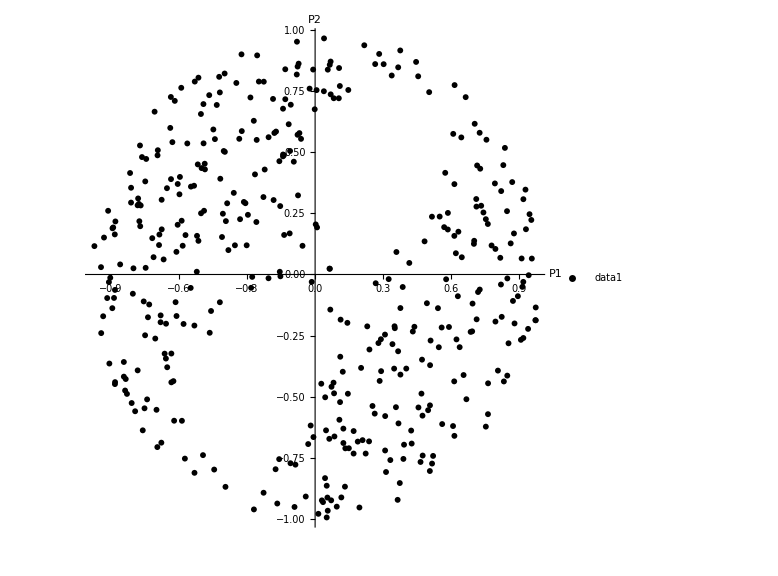
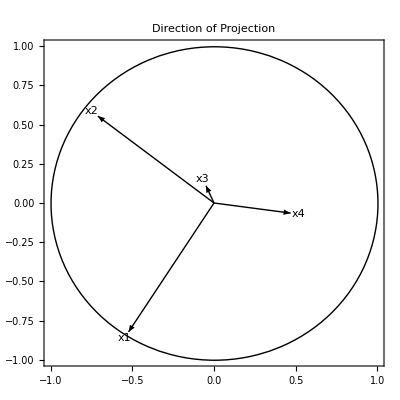
-Graphics- | -Graphics-

```mathematica
SlicePlot[{z20Data},A3old,{0,0,0,0},0.12,{Black, Red, Blue}]
```

A plot where you can dynamically change the slice.

```mathematica
SliceDynamic[z20Data,A3old,{0,0,0,0},0.12,{0, 1}]
```

```mathematica
A3=Transpose[Orthogonalize[Transpose[{
{RandomReal[{-1, 1}],RandomReal[{-1, 1}]},{RandomReal[{-1, 1}],RandomReal[{-1, 1}]},
{RandomReal[{-1, 1}],RandomReal[{-1, 1}]},
{RandomReal[{-1, 1}],RandomReal[{-1, 1}]}
}]]];
```

```mathematica
SliceDynamic[z20Datain,A3,{0,0,0,0},0.12,{0, 1}]
```

```mathematica
To compare with traditional visualisation of a 3 d object
```

3 a compare d object of To traditional visualisation with

## Generate 3 d objects and compare

```mathematica
in3d={}
{}
out3d={}
{}
in3d2={}
{}
out3d2={}
{}
genpt[ii_]:=Module[{y1,y2,y3,Reg,Regin,pt,aux,i},
Reg=ImplicitRegion[y1^2+y2^2+y3^2≤1,{y1,y2,y3}];
Regin=ImplicitRegion[(y1-0.1)^2+(y2+0.2)^2+(y3-0.6)^2≤.15,{y1,y2,y3}];
Reg2=ImplicitRegion[y1^6-5 y1^4 y2 y3+3 y1^4 y2^2+10 y1^2 y2^3 y3+3 y1^2 y2^4-y2^5 y3+y2^6+y3^6≤.03,{y1,y2,y3}];
pt=RandomPoint[Reg,10000];
For[i=1,i≤10000,i++,
If[RegionMember[Regin,pt[[i]]],in3d=Append[in3d,pt[[i]]],out3d=Append[out3d,pt[[i]]]]];
For[i=1,i≤10000,i++,
If[RegionMember[Reg2,pt[[i]]],in3d2=Append[in3d2,pt[[i]]],out3d2=Append[out3d2,pt[[i]]]]]
]
genpt[10000]
```

{}

{}

{}

«5 more identical outputs»

```mathematica
ListPointPlot3D[{out3d,in3d},PlotStyle->{Black,Red}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{out3d2,in3d2},PlotStyle->{Black,Red}]
```

-Graphics3D-

```mathematica
SliceDynamic[out3d,Transpose[Orthogonalize[RandomReal[{-1,1},{2,3}]]],ConstantArray[0,3],0.12,{0,1}]
```

```mathematica
SliceDynamic[out3d2,Transpose[Orthogonalize[RandomReal[{-1,1},{2,3}]]],ConstantArray[0,3],0.12,{0,1}]
```